## Define scaling and domain parameters

Note: For translationally invariant systems and quadratic domain with side 1000, rmax is 500.
rbin denotes the bin-size of spatial covariance data bins.

```mathematica
L=1.;
tmin =0;
tmax=200;
rmin = 0;
rmax=1000/2;
rbin = 10;
```

#### ϵ is set as 1/L

```mathematica
ϵ=SetPrecision[1/L,40];
```

# Handle input point pattern data

### Import snapshots data from files

#### Set the snapshot data file location

Note: On Windows computers, the file locations might need to be adjusted to include double forward slashes (//) instead of (/).
To change between “versions” (i.e. initial cell configurations), change  “v1” (ICC.1) to “v2” (ICC.2) or “v3” (ICC.3).

```mathematica
snapshotfilelocation=StringJoin[ParentDirectory[NotebookDirectory[]],"/snapshots/v1/run1/"];
```

#### Import data

```mathematica
scatterdataTime0=Import[StringJoin[snapshotfilelocation,"snap000001"],"Table","FieldSeparators"->" "];
scatterdataTimeMid=Import[StringJoin[snapshotfilelocation,"snap000100"],"Table","FieldSeparators"->" "];
scatterdataTimeEnd=Import[StringJoin[snapshotfilelocation,"snap000200"],"Table","FieldSeparators"->" "];
```

```mathematica
scatterdata1Time0=Select[scatterdataTime0,#[[1]] ==1&];
scatterdata2Time0=Select[scatterdataTime0,#[[1]] ==2&];
scatterdata1TimeMid=Select[scatterdataTimeMid,#[[1]] ==1&];
scatterdata2TimeMid=Select[scatterdataTimeMid,#[[1]] ==2&];
scatterdata1TimeEnd=Select[scatterdataTimeEnd,#[[1]] ==1&];
scatterdata2TimeEnd=Select[scatterdataTimeEnd,#[[1]] ==2&];
```

### Plot snapshots data

#### Set plot and label styles

```mathematica
snapshotPlotOps = {
PlotStyle->{{Red,PointSize[0.015]},{Green,PointSize[0.015]}},
AspectRatio->Automatic,
PlotRange->{{0,1000},{0,1000}},
Frame->True,
Axes-> True,
AxesLabel-> {"x","y"},
PlotLegends->Placed[{"s_1","s_2"},Right]
};
```

```mathematica
snapshotLabelOps = {
DisplayForm@RowBox[{SubscriptBox["x","1"]}],DisplayForm@RowBox[{SubscriptBox["x","2"]}],
LabelStyle->(FontSize->10)
};
```

#### Create snapshot scatter plots

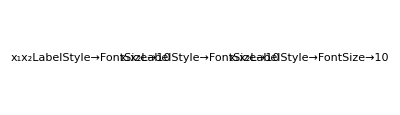

```mathematica
snapStart=Labeled[
ListPlot[
{scatterdata1Time0[[All,2;;3]],scatterdata2Time0[[All,2;;3]]},
snapshotPlotOps,
PlotLabel->"Time: 0 Δt"],
snapshotLabelOps,{Bottom,Left}
];
snapMid=Labeled[
ListPlot[
{scatterdata1TimeMid[[All,2;;3]],scatterdata2TimeMid[[All,2;;3]]},
snapshotPlotOps,
PlotLabel->"Time: 100 Δt"],
snapshotLabelOps,{Bottom,Left}
];
snapEnd=Labeled[
ListPlot[
{scatterdata1TimeEnd[[All,2;;3]],scatterdata2TimeEnd[[All,2;;3]]},
snapshotPlotOps,
PlotLabel->"Time: 200 Δt"],
snapshotLabelOps,{Bottom,Left}
];
GraphicsRow[{snapStart,snapMid, snapEnd}]
```

## Import and plot spatio-temporal cumulant data

### Import spatio-temporal cumulant data from files

#### Set the spatio-temporal cumulant data file location

To change between "versions" (i . e . initial cell configurations), change  "v1" (ICC .1) to "v2" (ICC .2) or "v3" (ICC .3) .

```mathematica
cumulantdatafilelocation=StringJoin[ParentDirectory[NotebookDirectory[]],"/cumulant_data/v1/no_drug_time_0_to_200/"];
```

#### Mean density data

```mathematica
dataDensity1mean=Import[StringJoin[cumulantdatafilelocation,"u1data_1_mean.csv"]];
dataDensity2mean=Import[StringJoin[cumulantdatafilelocation,"u1data_2_mean.csv"]];
```

#### Standard-deviation density data

```mathematica
dataDensity1std=Import[StringJoin[cumulantdatafilelocation,"u1data_1_std.csv"]];
dataDensity2std=Import[StringJoin[cumulantdatafilelocation,"u1data_2_std.csv"]];
```

#### Minimum and maximum density data

```mathematica
dataDensity1min=Import[StringJoin[cumulantdatafilelocation,"u1data_1_min.csv"]];
dataDensity2min=Import[StringJoin[cumulantdatafilelocation,"u1data_2_min.csv"]];

dataDensity1max=Import[StringJoin[cumulantdatafilelocation,"u1data_1_max.csv"]];
dataDensity2max=Import[StringJoin[cumulantdatafilelocation,"u1data_2_max.csv"]];
```

#### Mean spatial covariance data at the initial, middle and last time point for pair-wise combinations of the subpopulations

```mathematica
dataSpatialCov11meanTime0=Import[StringJoin[cumulantdatafilelocation,"u2data_11_mean_time0.csv"]];
dataSpatialCov12meanTime0=Import[StringJoin[cumulantdatafilelocation,"u2data_12_mean_time0.csv"]];
dataSpatialCov22meanTime0=Import[StringJoin[cumulantdatafilelocation,"u2data_22_mean_time0.csv"]];
```

```mathematica
dataSpatialCov11meanTimeMid=Import[StringJoin[cumulantdatafilelocation,"u2data_11_mean_time100.csv"]];
dataSpatialCov12meanTimeMid=Import[StringJoin[cumulantdatafilelocation,"u2data_12_mean_time100.csv"]];
dataSpatialCov22meanTimeMid=Import[StringJoin[cumulantdatafilelocation,"u2data_22_mean_time100.csv"]];
```

```mathematica
dataSpatialCov11meanTimeEnd=Import[StringJoin[cumulantdatafilelocation,"u2data_11_mean_time200.csv"]];
dataSpatialCov12meanTimeEnd=Import[StringJoin[cumulantdatafilelocation,"u2data_12_mean_time200.csv"]];
dataSpatialCov22meanTimeEnd=Import[StringJoin[cumulantdatafilelocation,"u2data_22_mean_time200.csv"]];
```

#### Minimum and maximum spatial covariances data at the middle and last time point for pair-wise combinations of the subpopulations

```mathematica
dataSpatialCov11minTimeMid=Import[StringJoin[cumulantdatafilelocation,"u2data_11_min_time100.csv"]];
dataSpatialCov12minTimeMid=Import[StringJoin[cumulantdatafilelocation,"u2data_12_min_time100.csv"]];
dataSpatialCov22minTimeMid=Import[StringJoin[cumulantdatafilelocation,"u2data_22_min_time100.csv"]];

dataSpatialCov11maxTimeMid=Import[StringJoin[cumulantdatafilelocation,"u2data_11_max_time100.csv"]];
dataSpatialCov12maxTimeMid=Import[StringJoin[cumulantdatafilelocation,"u2data_12_max_time100.csv"]];
dataSpatialCov22maxTimeMid=Import[StringJoin[cumulantdatafilelocation,"u2data_22_max_time100.csv"]];

dataSpatialCov11minTimeEnd=Import[StringJoin[cumulantdatafilelocation,"u2data_11_min_time200.csv"]];
dataSpatialCov12minTimeEnd=Import[StringJoin[cumulantdatafilelocation,"u2data_12_min_time200.csv"]];
dataSpatialCov22minTimeEnd=Import[StringJoin[cumulantdatafilelocation,"u2data_22_min_time200.csv"]];

dataSpatialCov11maxTimeEnd=Import[StringJoin[cumulantdatafilelocation,"u2data_11_max_time200.csv"]];
dataSpatialCov12maxTimeEnd=Import[StringJoin[cumulantdatafilelocation,"u2data_12_max_time200.csv"]];
dataSpatialCov22maxTimeEnd=Import[StringJoin[cumulantdatafilelocation,"u2data_22_max_time200.csv"]];
```

### Interpolate spatio-temporal cumulant data into functions

#### Density data

```mathematica
ddensity1mean=Interpolation[dataDensity1mean,InterpolationOrder->1];
ddensity2mean=Interpolation[dataDensity2mean,InterpolationOrder->1];
ddensity1std=Interpolation[dataDensity1std,InterpolationOrder->1];
ddensity2std=Interpolation[dataDensity2std,InterpolationOrder->1];
ddensity1min=Interpolation[dataDensity1min,InterpolationOrder->1];
ddensity2min=Interpolation[dataDensity2min,InterpolationOrder->1];
ddensity1max=Interpolation[dataDensity1max,InterpolationOrder->1];
ddensity2max=Interpolation[dataDensity2max,InterpolationOrder->1];
```

#### Spatial covariance data

Time 0:

```mathematica
dSpatialCov11meanTime0=Interpolation[dataSpatialCov11meanTime0,InterpolationOrder->0];
dSpatialCov12meanTime0=Interpolation[dataSpatialCov12meanTime0,InterpolationOrder->0];
dSpatialCov22meanTime0=Interpolation[dataSpatialCov22meanTime0,InterpolationOrder->0];
```

Middle time point:

```mathematica
dSpatialCov11meanTimeMid=Interpolation[dataSpatialCov11meanTimeMid,InterpolationOrder->0];
dSpatialCov12meanTimeMid=Interpolation[dataSpatialCov12meanTimeMid,InterpolationOrder->0];
dSpatialCov22meanTimeMid=Interpolation[dataSpatialCov22meanTimeMid,InterpolationOrder->0];

dSpatialCov11minTimeMid=Interpolation[dataSpatialCov11minTimeMid,InterpolationOrder->0];
dSpatialCov12minTimeMid=Interpolation[dataSpatialCov12minTimeMid,InterpolationOrder->0];
dSpatialCov22minTimeMid=Interpolation[dataSpatialCov22minTimeMid,InterpolationOrder->0];

dSpatialCov11maxTimeMid=Interpolation[dataSpatialCov11maxTimeMid,InterpolationOrder->0];
dSpatialCov12maxTimeMid=Interpolation[dataSpatialCov12maxTimeMid,InterpolationOrder->0];
dSpatialCov22maxTimeMid=Interpolation[dataSpatialCov22maxTimeMid,InterpolationOrder->0];
```

Final time point:

```mathematica
dSpatialCov11meanTimeEnd=Interpolation[dataSpatialCov11meanTimeEnd,InterpolationOrder->0];
dSpatialCov12meanTimeEnd=Interpolation[dataSpatialCov12meanTimeEnd,InterpolationOrder->0];
dSpatialCov22meanTimeEnd=Interpolation[dataSpatialCov22meanTimeEnd,InterpolationOrder->0];

dSpatialCov11minTimeEnd=Interpolation[dataSpatialCov11minTimeEnd,InterpolationOrder->0];
dSpatialCov12minTimeEnd=Interpolation[dataSpatialCov12minTimeEnd,InterpolationOrder->0];
dSpatialCov22minTimeEnd=Interpolation[dataSpatialCov22minTimeEnd,InterpolationOrder->0];

dSpatialCov11maxTimeEnd=Interpolation[dataSpatialCov11maxTimeEnd,InterpolationOrder->0];
dSpatialCov12maxTimeEnd=Interpolation[dataSpatialCov12maxTimeEnd,InterpolationOrder->0];
dSpatialCov22maxTimeEnd=Interpolation[dataSpatialCov22maxTimeEnd,InterpolationOrder->0];
```

### Plot density data, here generated by the stochastic point process (SPP)

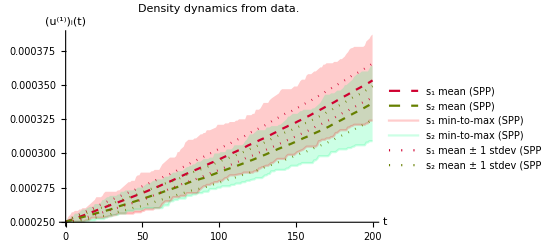

```mathematica
Plot[
{ddensity1mean[t],ddensity2mean[t], 
ddensity1min[t],ddensity2min[t],
ddensity1max[t],ddensity2max[t],
ddensity1mean[t]-ddensity1std[t],ddensity2mean[t]-ddensity1std[t],
ddensity1mean[t]+ddensity1std[t],ddensity2mean[t]+ddensity1std[t]
},
{t,0,tmax},
PlotStyle->{
{RGBColor[0.81,0.,0.19],Thick, Dashed},{RGBColor[0.4,0.5,0.],Thick,Dashed},
RGBColor[1,0,0,0.2],RGBColor[0,1,0.5,0.2],
None,None,
{RGBColor[0.81,0.,0.19],Thick, Dotted},{RGBColor[0.4,0.5,0.],Thick,Dotted},
{RGBColor[0.81,0.,0.19],Thick, Dotted},{RGBColor[0.4,0.5,0.],Thick,Dotted}
},
Filling->{ {3->{{5},RGBColor[1,0,0,0.2]}} ,{4->{{6},RGBColor[0,1,0.5,0.2]}} },
FillingStyle->Automatic,
PlotLegends->Placed[{ 
"s_1 mean (SPP)","s_2 mean (SPP)",
"s_1 min-to-max (SPP)","s_2 min-to-max (SPP)",
None,None,
"s_1 mean ± 1 stdev (SPP)","s_2 mean ± 1 stdev (SPP)",
None,None
},Right],
AxesLabel->{"t", "(u^(1))_i(t)"},
PlotRange->Full,
PlotLabel->StringForm["Density dynamics from data."] 
]
```

### Plot spatial covariance data, here generated by the stochastic point process (SPP)

```mathematica
spatialCovDataPotOps ={};
```

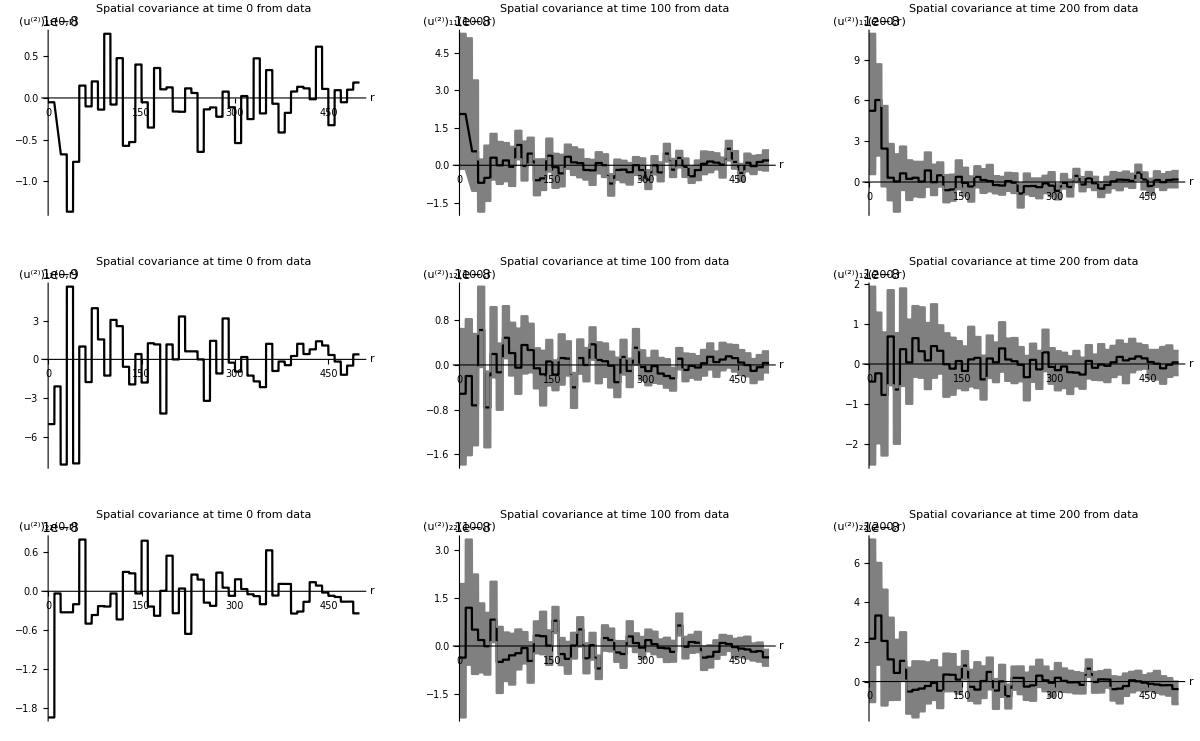

```mathematica
plot11T0=Plot[{dSpatialCov11meanTime0[r]},{r,0,rmax},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->"Spatial covariance at time 0 from data", AxesLabel->{"r","(u^(2))_11(0,r)"},PlotStyle->{Black}];
plot12T0=Plot[{dSpatialCov12meanTime0[r]},{r,0,rmax},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->"Spatial covariance at time 0 from data", AxesLabel->{"r","(u^(2))_12(0,r)"},PlotStyle->{Black}];
plot22T0=Plot[{dSpatialCov22meanTime0[r]},{r,0,rmax},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->"Spatial covariance at time 0 from data", AxesLabel->{"r","(u^(2))_22(0,r)"},PlotStyle->{Black}];

plot11TMid=Plot[{dSpatialCov11meanTimeMid[r],dSpatialCov11minTimeMid[r],dSpatialCov11maxTimeMid[r]},{r,0,rmax},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->"Spatial covariance at time 100 from data", AxesLabel->{"r","(u^(2))_11(100,r)"},PlotStyle->{Black,Gray,Gray},Filling->{ {2->{{3},Gray}} }];
plot12TMid=Plot[{dSpatialCov12meanTimeMid[r],dSpatialCov12minTimeMid[r],dSpatialCov12maxTimeMid[r]},{r,0,rmax},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->"Spatial covariance at time 100 from data", AxesLabel->{"r","(u^(2))_12(100,r)"},PlotStyle->{Black,Gray,Gray},Filling->{ {2->{{3},Gray}} }];
plot22TMid=Plot[{dSpatialCov22meanTimeMid[r],dSpatialCov22minTimeMid[r],dSpatialCov22maxTimeMid[r]},{r,0,rmax},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->"Spatial covariance at time 100 from data", AxesLabel->{"r","(u^(2))_22(100,r)"},PlotStyle->{Black,Gray,Gray},Filling->{ {2->{{3},Gray}} }];

plot11TEnd=Plot[{dSpatialCov11meanTimeEnd[r],dSpatialCov11minTimeEnd[r],dSpatialCov11maxTimeEnd[r]},{r,0,rmax},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->"Spatial covariance at time 200 from data", AxesLabel->{"r","(u^(2))_11(200,r)"},PlotStyle->{Black,Gray,Gray},Filling->{ {2->{{3},Gray}} }];
plot12TEnd=Plot[{dSpatialCov12meanTimeEnd[r],dSpatialCov12minTimeEnd[r],dSpatialCov12maxTimeEnd[r]},{r,0,rmax},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->"Spatial covariance at time 200 from data", AxesLabel->{"r","(u^(2))_12(200,r)"},PlotStyle->{Black,Gray,Gray},Filling->{ {2->{{3},Gray}} }];
plot22TEnd=Plot[{dSpatialCov22meanTimeEnd[r],dSpatialCov22minTimeEnd[r],dSpatialCov22maxTimeEnd[r]},{r,0,rmax},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->"Spatial covariance at time 200 from data", AxesLabel->{"r","(u^(2))_22(200,r)"},PlotStyle->{Black,Gray,Gray},Filling->{ {2->{{3},Gray}} }];

GraphicsGrid[{
{plot11T0,plot11TMid,plot11TEnd},
{plot12T0,plot12TMid,plot12TEnd},
{plot22T0,plot22TMid,plot22TEnd}
}]
```

# Formulate spatio-temporal cumulant (and mean-field) equations

## Set the initial conditions (ICs)

### Set the initial mean-field densities from input density data

```mathematica
defaultICqs = {ICq1->ddensity1mean[0], ICq2->ddensity2mean[0]};
```

### Set the initial corrections to mean-field densities to zero

```mathematica
defaultICps = {ICp1->0, ICp2->0};
```

### Set the initial conditions G_ij by Hankel-transforming spatial covariance input data

#### Set (u^(2))_ij(0,r) coefficients from input data

```mathematica
coeffs11=dataSpatialCov11meanTime0[[All, 2]];
coeffs12=dataSpatialCov12meanTime0[[All, 2]];
coeffs22=dataSpatialCov22meanTime0[[All, 2]];
```

#### Hankel transform functions g_ij(0,ϵr) to find the initial conditions G_ij(0,k)

Note:  ϵ has been included as a scaling parameter to rbin

```mathematica
HankelTransformOfInitialg11[k_] := Sum[ coeffs11[[i]]((i (rbin*ϵ))  BesselJ[1,2 i (rbin*ϵ) Pi k ]/k- 
((i-1)(rbin*ϵ)) BesselJ[1,2(i-1) (rbin*ϵ) Pi k]/k),
{i,1,Length[coeffs11]}];

HankelTransformOfInitialg12[k_] := Sum[ coeffs12[[i]]((i (rbin*ϵ))  BesselJ[1,2 i (rbin*ϵ) Pi k ]/k- 
((i-1)(rbin*ϵ)) BesselJ[1,2(i-1) (rbin*ϵ) Pi k]/k),
{i,1,Length[coeffs12]}];

HankelTransformOfInitialg22[k_] := Sum[ coeffs22[[i]]((i (rbin*ϵ))  BesselJ[1,2 i (rbin*ϵ) Pi k ]/k- 
((i-1)(rbin*ϵ)) BesselJ[1,2(i-1) (rbin*ϵ) Pi k]/k),
{i,1,Length[coeffs22]}];
```

```mathematica
defaultICGs = {ICG11->HankelTransformOfInitialg11[k],ICG12->HankelTransformOfInitialg12[k],ICG22->HankelTransformOfInitialg22[k]};
```

```mathematica
defaultICs=Union[defaultICqs, defaultICps,defaultICGs];
```

```mathematica
defaultDeath = {d1-> 0,d2->0};
```

#### Hankel transform functions g_ij(0,ϵr) to find the end values G_ij(200,k)

```mathematica
coeffs11end=dataSpatialCov11meanTimeEnd[[All, 2]];
coeffs12end=dataSpatialCov12meanTimeEnd[[All, 2]];

HankelTransformOfFinalg11[k_] := Sum[ coeffs11end[[i]]((i (rbin*ϵ))  BesselJ[1,2 i (rbin*ϵ) Pi k ]/k- 
((i-1)(rbin*ϵ)) BesselJ[1,2(i-1) (rbin*ϵ) Pi k]/k),
{i,1,Length[coeffs11end]}];

HankelTransformOfFinalg12[k_] := Sum[ coeffs12end[[i]]((i (rbin*ϵ))  BesselJ[1,2 i (rbin*ϵ) Pi k ]/k- 
((i-1)(rbin*ϵ)) BesselJ[1,2(i-1) (rbin*ϵ) Pi k]/k),
{i,1,Length[coeffs12end]}];
```

## Define model parameters and equations

### Define the model parameters for reactant-catalyst-product processes

#### Cell division

```mathematica
totIntB1=0.001;
totIntB11=0.025;
totIntB12=0.05;
σB1=25;
σB11=25;
σB12=25;

kernelB1 = {B1->   (totIntB1 Exp[-2 π^2  (#)^2 σB1^2] &) };
kernelB11 ={B11 -> (totIntB11 Exp[-2 π^2 (#)^2 σB11^2] &) };
kernelB12 ={B12 -> (totIntB12 Exp[-2 π^2 (#)^2 σB12^2] &) };
```

#### Cell death

Note: In the worked example, death parameters are defined by analytically derived rules (not set).

#### Cell-cell communication via growth hormones

```mathematica
totIntH =100;
σH=100;
kernelH ={H-> ( totIntH Exp[-2  π^2  (#)^2 σH^2] &) };
```

#### Gather the kernel rules

```mathematica
kernelrules = Flatten[{kernelB1,kernelB11,kernelB12,kernelH}];
```

### Model equations

#### Mean-field density dynamics

```mathematica
eqq1 ={D[q1[t],t]==
-d1 q1[t]+totIntB1 q1[t]+totIntB11 totIntH q1[t]^2,
q1[0]==ICq1} /. kernelrules;
```

```mathematica
eqq2 ={D[q2[t],t]==
-d2 q2[t]+totIntB12 totIntH q1[t] q2[t],
q2[0]==ICq2} /. kernelrules;
```

#### Correction to mean-field density dynamics

```mathematica
eqp1 ={D[p1[t],t]== 
W11[t]-d1 p1[t]+totIntB1 p1[t]+2 totIntB11 totIntH p1[t] q1[t],
p1[0]==ICp1} /. kernelrules;
```

```mathematica
eqp2 ={D[p2[t],t]==
W12[t]-d2 p2[t]+totIntB12 totIntH (p2[t] q1[t]+p1[t] q2[t]),
p2[0]==ICp2} /. kernelrules;
```

#### Spatial covariance dynamics

```mathematica
eqG11= {D[G11[t,k],t]==
-2 d1 G11[t,k]+2 B1[k] G11[t,k]+2 B1[k] q1[t]+2 totIntH B1[k] G11[t,k] q1[t]+2 B1[k] G11[t,k] H[k] q1[t]+(2 totIntH B1[k]+2 B1[k] H[k]) q1[t]^2,G11[0,k]==ICG11} /. kernelrules;
```

```mathematica
eqG12= {D[G12[t,k],t]==
-d1 G12[t,k]-d2 G12[t,k]+B1[k] G12[t,k]+totIntH B1[k] G12[t,k] q1[t]+B1[k] G12[t,k] H[k] q1[t]+totIntH G12[t,k] q1[t] B12[k]+G11[t,k] H[k] q2[t] B12[k]+H[k] q1[t] q2[t] B12[k],G12[0,k]==ICG12} /. kernelrules;
```

```mathematica
eqG22= {D[G22[t,k],t]==
-2 d2 G22[t,k]+2 totIntH G22[t,k] q1[t] B12[k]+2 G12[t,k] H[k] q2[t] B12[k]+2 totIntH q1[t] q2[t] B12[k],G22[0,k]==ICG22} /. kernelrules;
```

#### Evaluate the auxiliary functions W_11 and W_12 at time 0

```mathematica
kmin = 10^-20;
kmax =0.02;
```

Note 1: In order to test the suitability of our chosen upper integration bound kmax, we plot the  integrands of W_11(t=0,k) and W_12(t=0,k).
Note 2: kmin is chosen to be a non-zero value in order to avoid problems with the exact Hankel-transform of piece-wise step functions.

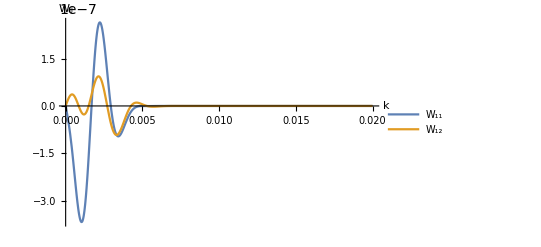

```mathematica
W11[k]= 2π NIntegrate[k*totIntB11*HankelTransformOfInitialg11[k]*(H[k]/.kernelrules),{k,0,kmax}];
W12[k]= 2π NIntegrate[k*totIntB12*HankelTransformOfInitialg12[k]*(H[k]/.kernelrules),{k,0,kmax}];
Plot[{k*totIntB11*HankelTransformOfInitialg11[k]*(H[k]/.kernelrules),k*totIntB12*HankelTransformOfInitialg12[k]*(H[k]/.kernelrules)},{k,0,kmax},PlotRange-> All,AxesLabel->{"k","W_ij"},PlotLegends->{"W_11","W_12"}]
```

## Solve model equations

Note: Since p depends on W and q, and W depends on g, and g depends on q, we solve the equations in the following order:
(1) Mean-field density dynamics equations (eqq1, eqq2).
(2) Spatial covariance dynamics equations (procedeqG11, procedeqG12, procedeqG22).
(3) Auxiliary functions W (W11,W12).
(4) Correction density dynamics equations  (eqp1, eqp2).
Note: You may need to adjust solver-options for your application.

```mathematica
SolveModelEquations[deathrule0_, ICsrule0_]:= Module[{deathrule=deathrule0, ICsrule=ICsrule0},
procedeqq1 = eqq1 /.deathrule /.ICsrule;
procedeqq2 = eqq2 /.deathrule /.ICsrule;
procedeqp1 = eqp1 /.deathrule /.ICsrule;
procedeqp2 = eqp2 /.deathrule /.ICsrule;
procedeqG11 = eqG11 /.deathrule /.ICsrule;
procedeqG12 = eqG12 /.deathrule /.ICsrule;
procedeqG22 = eqG22 /.deathrule /.ICsrule;
qsols=Flatten[NDSolve[Flatten[{procedeqq1,procedeqq2}],{q1,q2},{t,0,tmax}]];
geqs =Union[procedeqG11,procedeqG12, procedeqG22]/.qsols;
maxcellmeasure = 0.0001;
gsols =
NDSolve[geqs,{G11,G12,G22},{t,tmin,tmax},{k,kmin,kmax}, AccuracyGoal->10, PrecisionGoal->20, Method->"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcellmeasure}}}] //Flatten;
ClearAll[W11];
W11[t_?NumericQ]:=2π NIntegrate[k*totIntB11*( G11[t,k]/.gsols)*(H[k]/.kernelrules), {k,kmin,kmax},WorkingPrecision->10,PrecisionGoal->3] ;
ClearAll[W12];
W12[t_?NumericQ]:=2π NIntegrate[k*totIntB12*( G12[t,k]/.gsols)*(H[k]/.kernelrules), {k,kmin,kmax},WorkingPrecision->10,PrecisionGoal->3] ;
peqs=Union[SetPrecision[procedeqp1,40],SetPrecision[procedeqp2,40]] /.qsols /.gsols;
psols = Flatten[NDSolve[peqs,{p1,p2}, {t,0,tmax},WorkingPrecision->10]];
{qsols, gsols, W11, W12,psols}
]
```

```mathematica
solsdefault=SolveModelEquations[defaultDeath, defaultICs];
```

# Compare SPP, MFPM and STCM generated dynamics in plots.

Abbreviations:
SPP: Stochastic point process.
MFPM: Mean-field population model.
STCM: Spatio-temporal cumulant model.

### Density dynamics

```mathematica
(** tickSpecification={ {0.00025,2.5},  {0.0003,3}, {0.00035,3.5}}; *)
```

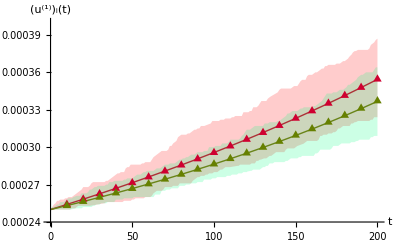

```mathematica
shadeplot=Plot[
{
ddensity1min[t],ddensity2min[t],
ddensity1max[t],ddensity2max[t],
},
{t,0,tmax},
PlotStyle->{None,None},
Filling->{ {1->{{3},RGBColor[1,0,0,0.2]}} ,{2->{{4},RGBColor[0,1,0.5,0.2]}} }
(**,PlotRange->{{0,200},{0.00024,0.00065}}*)
];
lineplot = Plot[
{
(q1[t]/. qsols), q2[t]/. qsols
},
{t,0,tmax},
PlotStyle->
{
{RGBColor[0.81,0.,0.19],Thick},{RGBColor[0.4,0.5,0.],Thick}
},
PlotRange->{{0,200},{0.00024,0.0004}},
LabelStyle->(FontSize->10),
(** Ticks->{Automatic,tickSpecification} ,*)
PlotRangeClipping->False,
AxesLabel->{"t", "(u^(1))_i(t)"}
(**Epilog->{
Text[Style["× 10^-4",11,Black],ImageScaled@{.14,.85}]
}*)
];

marksp1= Table[{t,(q1[t] /. qsols)+ ϵ^2(p1[t]/.psols)},{t,10,200,10}];
marksp2 = Table[{t,(q2[t] /. qsols)+ ϵ^2(p2[t]/.psols)},{t,10,200,10}];
markplot=ListPlot[
{marksp1,marksp2},
PlotMarkers->{{"▲",Small},{"▲",Small}},
PlotStyle->{RGBColor[0.81,0.,0.19],RGBColor[0.4,0.5,0.]}];


plotd1=Show[lineplot,shadeplot,markplot]
```

### Spatial covariance dynamics

```mathematica
tex=0;

invGfromSTCMg11Table =  Table[{r, 2 Pi * NIntegrate[(G11[tex,$k]/.gsols) *  BesselJ[0,2 * Pi * $k * r] * $k,{$k,kmin,kmax},PrecisionGoal->3,WorkingPrecision->40]} ,{r,0,500, 10}];
invGfromSTCMg11 = Interpolation[invGfromSTCMg11Table, InterpolationOrder->2];
plotSTCMg11T0 = Plot[invGfromSTCMg11[r],{r,0,500},PlotRange->All, PlotStyle->{Orange,Thick}];

invGfromSTCMg12Table =  Table[{r, 2 Pi * NIntegrate[(G12[tex,$k]/.gsols) *  BesselJ[0,2 * Pi * $k * r] * $k,{$k,kmin,kmax},PrecisionGoal->3,WorkingPrecision->40]} ,{r,0,500, 10}];
invGfromSTCMg12 = Interpolation[invGfromSTCMg12Table, InterpolationOrder->1];
plotSTCMg12T0= Plot[invGfromSTCMg12[r],{r,0,500},PlotRange->All, PlotStyle->{Orange,Thick}];

invGfromSTCMg22Table =  Table[{r, 2 Pi * NIntegrate[(G22[tex,$k]/.gsols) *  BesselJ[0,2 * Pi * $k * r] * $k,{$k,kmin,kmax},PrecisionGoal->3,WorkingPrecision->40]} ,{r,0,500, 10}];
invGfromSTCMg22 = Interpolation[invGfromSTCMg22Table, InterpolationOrder->2];
plotSTCMg22T0 = Plot[invGfromSTCMg22[r],{r,0,500},PlotRange->All, PlotStyle->{Orange,Thick}];
```

```mathematica
tex=100;

invGfromSTCMg11Table =  Table[{r, 2 Pi * NIntegrate[(G11[tex,$k]/.gsols) *  BesselJ[0,2 * Pi * $k * r] * $k,{$k,kmin,kmax},PrecisionGoal->3,WorkingPrecision->40]} ,{r,0,500, 10}];
invGfromSTCMg11 = Interpolation[invGfromSTCMg11Table, InterpolationOrder->2];
plotSTCMg11T00 = Plot[invGfromSTCMg11[r],{r,0,500},PlotRange->All, PlotStyle->{Orange,Thick}];

invGfromSTCMg12Table =  Table[{r, 2 Pi * NIntegrate[(G12[tex,$k]/.gsols) *  BesselJ[0,2 * Pi * $k * r] * $k,{$k,kmin,kmax},PrecisionGoal->3,WorkingPrecision->40]} ,{r,0,500, 10}];
invGfromSTCMg12 = Interpolation[invGfromSTCMg12Table, InterpolationOrder->1];
plotSTCMg12T100= Plot[invGfromSTCMg12[r],{r,0,500},PlotRange->All, PlotStyle->{Orange,Thick}];

invGfromSTCMg22Table =  Table[{r, 2 Pi * NIntegrate[(G22[tex,$k]/.gsols) *  BesselJ[0,2 * Pi * $k * r] * $k,{$k,kmin,kmax},PrecisionGoal->3,WorkingPrecision->40]} ,{r,0,500, 10}];
invGfromSTCMg22 = Interpolation[invGfromSTCMg22Table, InterpolationOrder->2];
plotSTCMg22T100 = Plot[invGfromSTCMg22[r],{r,0,500},PlotRange->All, PlotStyle->{Orange,Thick}];
```

```mathematica
tex=200;

invGfromSTCMg11Table =  Table[{r, 2 Pi * NIntegrate[(G11[tex,$k]/.gsols) *  BesselJ[0,2 * Pi * $k * r] * $k,{$k,kmin,kmax},PrecisionGoal->1,WorkingPrecision->10]} ,{r,0,500, 10}];
invGfromSTCMg11 = Interpolation[invGfromSTCMg11Table, InterpolationOrder->2];
plotSTCMg11T200 = Plot[invGfromSTCMg11[r],{r,0,500},PlotRange->All, PlotStyle->{Orange,Thick}];

invGfromSTCMg12Table =  Table[{r, 2 Pi * NIntegrate[(G12[tex,$k]/.gsols) *  BesselJ[0,2 * Pi * $k * r] * $k,{$k,kmin,kmax},PrecisionGoal->1,WorkingPrecision->10]} ,{r,0,500, 10}];
invGfromSTCMg12 = Interpolation[invGfromSTCMg12Table, InterpolationOrder->1];
plotSTCMg12T00 = Plot[invGfromSTCMg12[r],{r,0,500},PlotRange->All, PlotStyle->{Orange,Thick}];

invGfromSTCMg22Table =  Table[{r, 2 Pi * NIntegrate[(G22[tex,$k]/.gsols) *  BesselJ[0,2 * Pi * $k * r] * $k,{$k,kmin,kmax},PrecisionGoal->1,WorkingPrecision->10]} ,{r,0,500, 10}];
invGfromSTCMg22 = Interpolation[invGfromSTCMg22Table, InterpolationOrder->2];
plotSTCMg22T200 = Plot[invGfromSTCMg22[r],{r,0,500},PlotRange->All, PlotStyle->{Orange,Thick}];
```

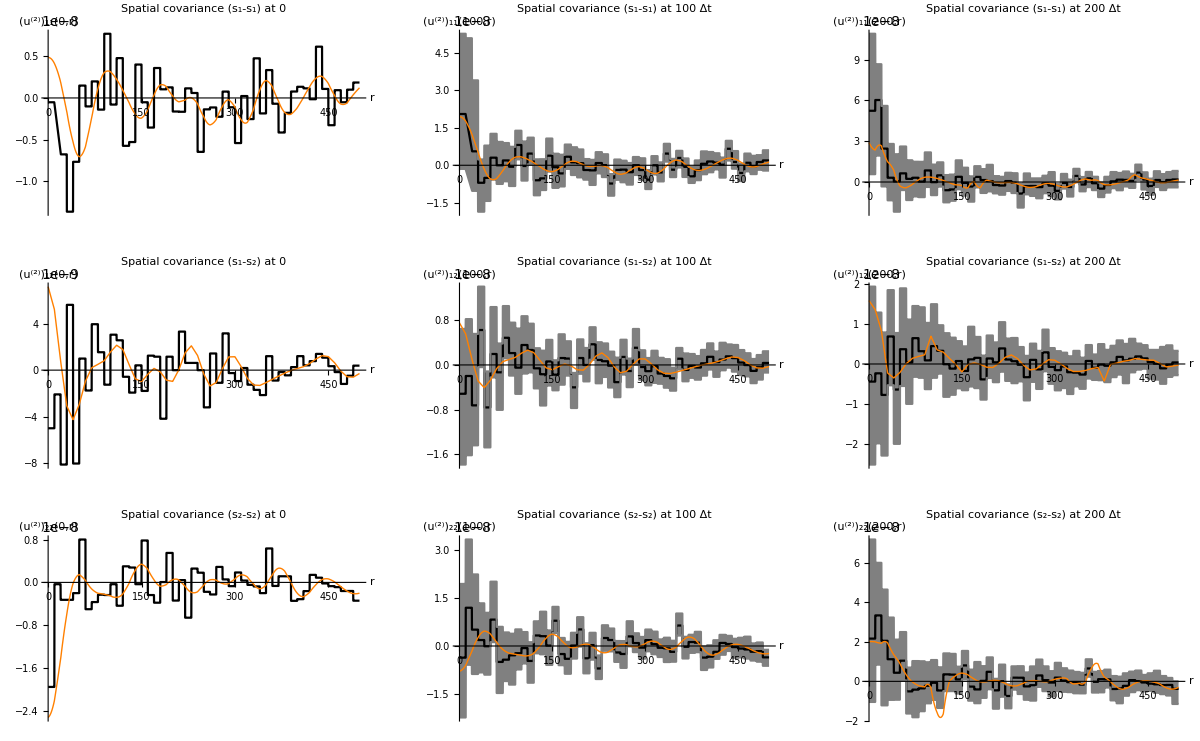

```mathematica
u2compICC3=GraphicsGrid[{
{Show[plot11T0,plotSTCMg11T0,PlotRange-> All,PlotLabel-> "Spatial covariance (s_1-s_1) at 0",LabelStyle->(FontSize->16)],
Show[plot11TMid,plotSTCMg11T00,PlotRange-> All,PlotLabel-> "Spatial covariance (s_1-s_1) at 100 Δt",LabelStyle->(FontSize->16)],
Show[plot11TEnd,plotSTCMg11T200,PlotRange-> All, PlotLabel-> "Spatial covariance (s_1-s_1) at 200 Δt",LabelStyle->(FontSize->16)]},
{Show[plot12T0,plotSTCMg12T0,PlotRange-> All,PlotLabel-> "Spatial covariance (s_1-s_2) at 0",LabelStyle->(FontSize->16)],
Show[plot12TMid,plotSTCMg12T100,PlotRange-> All,PlotLabel-> "Spatial covariance (s_1-s_2) at 100 Δt",LabelStyle->(FontSize->16)],
Show[plot12TEnd,plotSTCMg12T00 ,PlotRange-> All,PlotLabel-> "Spatial covariance (s_1-s_2) at 200 Δt",LabelStyle->(FontSize->16)]},
{Show[plot22T0,plotSTCMg22T0,PlotRange-> All,PlotLabel-> "Spatial covariance (s_2-s_2) at 0",LabelStyle->(FontSize->16)],
Show[plot22TMid,plotSTCMg22T100,PlotRange-> All,PlotLabel-> "Spatial covariance (s_2-s_2) at 100 Δt",LabelStyle->(FontSize->16)],
Show[plot22TEnd,plotSTCMg22T200,PlotRange-> All,PlotLabel-> "Spatial covariance (s_2-s_2) at 200 Δt",LabelStyle->(FontSize->16)]}
}]
```